```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Remove[q1]
Remove[q2]
<<"/home/riccardo/Programs/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[20]}->{V[20]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/input/kinematics.m already exist. It will NOT be overwritten.

Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/input/kinematics.m.

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

```mathematica
process={V[20]}->{V[20]};
```

```mathematica
topologies1L=CreateTopologies[1,1-> 1,ExcludeTopologies->Tadpoles];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 6 Particles insertions

> Top. 2: 20 Particles insertions

Restoring 24 field point(s)

in total: 26 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 6 Particles amplitudes

> Top. 2: 20 Particles amplitudes

in total: 26 Particles amplitudes

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

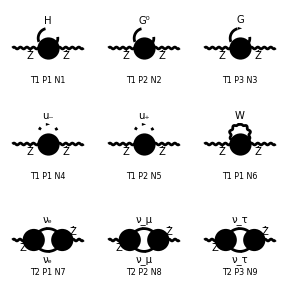

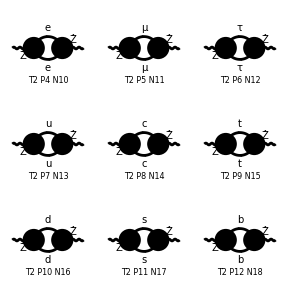

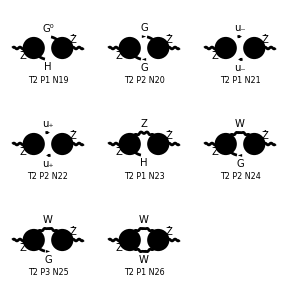

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L]; (*"Extracts from a FeynArts amplitude a list of amplitudes in the format understood by ABISS."*)
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/feynArts_amplitudes/OneLoopAmplitudes.m

```mathematica
FullForm[myAmp1L[[1]]]
```

Times[Complex[0,Rational[1,32]],Power[EL,2],gHHZZ,Power[Pi,-4],FeynAmpDenominator[PropagatorDenominator[FourMomentum[Internal,1],MH]],MetricTensor[Index[Lorentz,1],Index[Lorentz,2]],PolarizationVector[V[20],FourMomentum[Incoming,1],Index[Lorentz,1]],Conjugate[PolarizationVector][V[20],FourMomentum[Outgoing,1],Index[Lorentz,2]]]

```mathematica
myAmp1L[[1]]
```

(ⅈ EL^2 gHHZZ FeynAmpDenominator[1/(-MH^2+(q1)^2)] g[Lor1,Lor2] ep[V[20],p1,Lor1] ep^*[V[20],k1,Lor2])/(32 π^4)

```mathematica
myAmp1L[[1]]//FullForm
```

Times[Complex[0,Rational[1,32]],Power[EL,2],gHHZZ,Power[Pi,-4],FeynAmpDenominator[PropagatorDenominator[FourMomentum[Internal,1],MH]],MetricTensor[Index[Lorentz,1],Index[Lorentz,2]],PolarizationVector[V[20],FourMomentum[Incoming,1],Index[Lorentz,1]],Conjugate[PolarizationVector][V[20],FourMomentum[Outgoing,1],Index[Lorentz,2]]]

## Longitudinal and Transverse Part

### Projectors

```mathematica
l[Lor1_,Lor2_]:=-SP[p1,{Lor1}]SP[p1,{Lor2}]/SP[p1,p1]
```

```mathematica
t[Lor1_,Lor2_]:=(-SP[{Lor1},{Lor2}]+SP[p1,{Lor1}]SP[p1,{Lor2}]/SP[p1,p1])/(d-1)
```

### Remove polarization vectors

```mathematica
removePolarizationVectors={PolarizationVector[V[20],p_,i_]->1,Conjugate[PolarizationVector][V[20],p_,i_]->1}
```

{ep[V[20],p_,i_]→1,ep^*[V[20],p_,i_]→1}

## Interference

```mathematica
myAmp1LABISS=Map[AmpSquare[#,1]&,myAmp1L];
```

```mathematica
myAmp1LnoEP=myAmp1LABISS/.removePolarizationVectors;
```

```mathematica
myAmp1LLongitudinal=Map[AmpSquare[#*l[Lor1,Lor2],1]&,myAmp1LnoEP];
```

```mathematica
SquareSimplifyAndSave[myAmp1LLongitudinal,{1}]
```

Computed contribution 1-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_1_1.m.

Computed contribution 2-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_2_1.m.

Computed contribution 3-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_3_1.m.

Computed contribution 4-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_4_1.m.

Computed contribution 5-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_5_1.m.

Computed contribution 6-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_6_1.m.

Computed contribution 7-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_7_1.m.

Computed contribution 8-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_8_1.m.

Computed contribution 9-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_9_1.m.

Computed contribution 10-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_10_1.m.

Computed contribution 11-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_11_1.m.

Computed contribution 12-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_12_1.m.

Computed contribution 13-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_13_1.m.

Computed contribution 14-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_14_1.m.

Computed contribution 15-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_15_1.m.

Computed contribution 16-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_16_1.m.

Computed contribution 17-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_17_1.m.

Computed contribution 18-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_18_1.m.

Computed contribution 19-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_19_1.m.

Computed contribution 20-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_20_1.m.

Computed contribution 21-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_21_1.m.

Computed contribution 22-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_22_1.m.

Computed contribution 23-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_23_1.m.

Computed contribution 24-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_24_1.m.

Computed contribution 25-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_25_1.m.

Computed contribution 26-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ//interferences/Contribution_26_1.m.

## Shift

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/input/kinematics.m.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,26},{j,1}]
```

Integral family {{B0, {MH}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_1_1.m.

Integral family {{B0, {MZ}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_2_1.m.

Integral family {{B0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_3_1.m.

Integral family {{B0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_4_1.m.

Integral family {{B0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_5_1.m.

Integral family {{B0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_6_1.m.

Integral family {{A0, {0}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_7_1.m.

Integral family {{A0, {0}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_8_1.m.

Integral family {{A0, {0}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_9_1.m.

Integral family {{B0, {ME}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_10_1.m.

Integral family {{B0, {MM}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_11_1.m.

Integral family {{B0, {ML}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_12_1.m.

Integral family {{B0, {MU}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_13_1.m.

Integral family {{B0, {MC}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_14_1.m.

Integral family {{B0, {MT}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_15_1.m.

Integral family {{B0, {MD}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_16_1.m.

Integral family {{B0, {MS}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_17_1.m.

Integral family {{B0, {MB}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_18_1.m.

Integral family {{C0, {MH, MZ}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_19_1.m.

Integral family {{B0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_20_1.m.

Integral family {{B0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_21_1.m.

Integral family {{B0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_22_1.m.

Integral family {{C0, {MH, MZ}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_23_1.m.

Integral family {{B0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_24_1.m.

Integral family {{B0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_25_1.m.

Integral family {{B0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/interferences/Contribution_26_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,26},{j,1}]
```

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_1_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_2_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_3_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_4_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_5_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_6_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_7_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_8_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_9_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_10_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_11_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_12_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_13_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_14_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_15_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_16_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_17_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_18_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_19_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_20_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_21_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_22_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_23_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_24_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_25_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/ZZ/kira_input/Contribution_26_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[B0,{MH},1,0],userIntegral[B0,{MZ},1,0],userIntegral[B0,{MW},1,0],userIntegral[A0,{0},0,1],userIntegral[A0,{0},1,0],userIntegral[A0,{0},1,1],userIntegral[A0,{0},-1,1],userIntegral[A0,{0},0,0],userIntegral[A0,{0},1,-1],userIntegral[B0,{ME},1,1],userIntegral[B0,{ME},0,1],userIntegral[B0,{ME},1,0],userIntegral[B0,{ME},-1,1],userIntegral[B0,{ME},0,0],userIntegral[B0,{ME},1,-1],userIntegral[B0,{MM},1,1],userIntegral[B0,{MM},0,1],userIntegral[B0,{MM},1,0],userIntegral[B0,{MM},-1,1],userIntegral[B0,{MM},0,0],userIntegral[B0,{MM},1,-1],userIntegral[B0,{ML},1,1],userIntegral[B0,{ML},0,1],userIntegral[B0,{ML},1,0],userIntegral[B0,{ML},-1,1],userIntegral[B0,{ML},0,0],userIntegral[B0,{ML},1,-1],userIntegral[B0,{MU},1,1],userIntegral[B0,{MU},0,1],userIntegral[B0,{MU},1,0],userIntegral[B0,{MU},-1,1],userIntegral[B0,{MU},0,0],userIntegral[B0,{MU},1,-1],userIntegral[B0,{MC},1,1],userIntegral[B0,{MC},0,1],userIntegral[B0,{MC},1,0],userIntegral[B0,{MC},-1,1],userIntegral[B0,{MC},0,0],userIntegral[B0,{MC},1,-1],userIntegral[B0,{MT},1,1],userIntegral[B0,{MT},0,1],userIntegral[B0,{MT},1,0],userIntegral[B0,{MT},-1,1],userIntegral[B0,{MT},0,0],userIntegral[B0,{MT},1,-1],userIntegral[B0,{MD},1,1],userIntegral[B0,{MD},0,1],userIntegral[B0,{MD},1,0],userIntegral[B0,{MD},-1,1],userIntegral[B0,{MD},0,0],userIntegral[B0,{MD},1,-1],userIntegral[B0,{MS},1,1],userIntegral[B0,{MS},0,1],userIntegral[B0,{MS},1,0],userIntegral[B0,{MS},-1,1],userIntegral[B0,{MS},0,0],userIntegral[B0,{MS},1,-1],userIntegral[B0,{MB},1,1],userIntegral[B0,{MB},0,1],userIntegral[B0,{MB},1,0],userIntegral[B0,{MB},-1,1],userIntegral[B0,{MB},0,0],userIntegral[B0,{MB},1,-1],userIntegral[C0,{MH,MZ},1,1],userIntegral[C0,{MH,MZ},0,1],userIntegral[C0,{MH,MZ},1,0],userIntegral[C0,{MH,MZ},-1,1],userIntegral[C0,{MH,MZ},0,0],userIntegral[C0,{MH,MZ},1,-1],userIntegral[B0,{MW},1,1],userIntegral[B0,{MW},0,1],userIntegral[B0,{MW},-1,1],userIntegral[B0,{MW},0,0],userIntegral[B0,{MW},1,-1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[A0,{0},0,1]→0,userIntegral[A0,{0},1,0]→0,userIntegral[A0,{0},-1,1]→0,userIntegral[A0,{0},0,0]→0,userIntegral[A0,{0},1,-1]→0,userIntegral[B0,{m1},0,0]→0,userIntegral[C0,{m1,m2},0,0]→0,userIntegral[B0,{m1},0,1]→userIntegral[B0,{m1},1,0],userIntegral[B0,{m1},-1,1]→psq userIntegral[B0,{m1},1,0],userIntegral[B0,{m1},1,-1]→psq userIntegral[B0,{m1},1,0],userIntegral[C0,{m1,m2},1,0]→userIntegral[B0,{m1},1,0],userIntegral[C0,{m1,m2},-1,1]→(-m1^2+m2^2+psq) userIntegral[C0,{m1,m2},0,1],userIntegral[C0,{m1,m2},1,-1]→(m1^2-m2^2+psq) userIntegral[B0,{m1},1,0]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[B0,{MH},1,0],userIntegral[B0,{MZ},1,0],userIntegral[B0,{MW},1,0],userIntegral[A0,{0},0,1],userIntegral[A0,{0},1,0],userIntegral[A0,{0},1,1],userIntegral[A0,{0},-1,1],userIntegral[A0,{0},0,0],userIntegral[A0,{0},1,-1],userIntegral[B0,{ME},1,1],userIntegral[B0,{ME},0,1],userIntegral[B0,{ME},1,0],userIntegral[B0,{ME},-1,1],userIntegral[B0,{ME},0,0],userIntegral[B0,{ME},1,-1],userIntegral[B0,{MM},1,1],userIntegral[B0,{MM},0,1],userIntegral[B0,{MM},1,0],userIntegral[B0,{MM},-1,1],userIntegral[B0,{MM},0,0],userIntegral[B0,{MM},1,-1],userIntegral[B0,{ML},1,1],userIntegral[B0,{ML},0,1],userIntegral[B0,{ML},1,0],userIntegral[B0,{ML},-1,1],userIntegral[B0,{ML},0,0],userIntegral[B0,{ML},1,-1],userIntegral[B0,{MU},1,1],userIntegral[B0,{MU},0,1],userIntegral[B0,{MU},1,0],userIntegral[B0,{MU},-1,1],userIntegral[B0,{MU},0,0],userIntegral[B0,{MU},1,-1],userIntegral[B0,{MC},1,1],userIntegral[B0,{MC},0,1],userIntegral[B0,{MC},1,0],userIntegral[B0,{MC},-1,1],userIntegral[B0,{MC},0,0],userIntegral[B0,{MC},1,-1],userIntegral[B0,{MT},1,1],userIntegral[B0,{MT},0,1],userIntegral[B0,{MT},1,0],userIntegral[B0,{MT},-1,1],userIntegral[B0,{MT},0,0],userIntegral[B0,{MT},1,-1],userIntegral[B0,{MD},1,1],userIntegral[B0,{MD},0,1],userIntegral[B0,{MD},1,0],userIntegral[B0,{MD},-1,1],userIntegral[B0,{MD},0,0],userIntegral[B0,{MD},1,-1],userIntegral[B0,{MS},1,1],userIntegral[B0,{MS},0,1],userIntegral[B0,{MS},1,0],userIntegral[B0,{MS},-1,1],userIntegral[B0,{MS},0,0],userIntegral[B0,{MS},1,-1],userIntegral[B0,{MB},1,1],userIntegral[B0,{MB},0,1],userIntegral[B0,{MB},1,0],userIntegral[B0,{MB},-1,1],userIntegral[B0,{MB},0,0],userIntegral[B0,{MB},1,-1],userIntegral[C0,{MH,MZ},1,1],userIntegral[C0,{MH,MZ},0,1],userIntegral[C0,{MH,MZ},1,0],userIntegral[C0,{MH,MZ},-1,1],userIntegral[C0,{MH,MZ},0,0],userIntegral[C0,{MH,MZ},1,-1],userIntegral[B0,{MW},1,1],userIntegral[B0,{MW},0,1],userIntegral[B0,{MW},-1,1],userIntegral[B0,{MW},0,0],userIntegral[B0,{MW},1,-1]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[B0,{MH},1,0],userIntegral[B0,{MZ},1,0],userIntegral[B0,{MW},1,0],userIntegral[A0,{0},1,1],userIntegral[B0,{ME},1,1],userIntegral[B0,{ME},1,0],userIntegral[B0,{MM},1,1],userIntegral[B0,{MM},1,0],userIntegral[B0,{ML},1,1],userIntegral[B0,{ML},1,0],userIntegral[B0,{MU},1,1],userIntegral[B0,{MU},1,0],userIntegral[B0,{MC},1,1],userIntegral[B0,{MC},1,0],userIntegral[B0,{MT},1,1],userIntegral[B0,{MT},1,0],userIntegral[B0,{MD},1,1],userIntegral[B0,{MD},1,0],userIntegral[B0,{MS},1,1],userIntegral[B0,{MS},1,0],userIntegral[B0,{MB},1,1],userIntegral[B0,{MB},1,0],userIntegral[C0,{MH,MZ},1,1],userIntegral[C0,{MH,MZ},0,1],userIntegral[B0,{MW},1,1]}

```mathematica
Do[
SaveResult[i,j];
,{i,26},{j,1}]
```

## Ward Identity Test

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,26}]
```

```mathematica
diagramCoefficients
```

{{-(ⅈ EL^2 gHHZZ)/(32 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-(ⅈ EL^2 gXXZZ)/(32 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-(ⅈ EL^2 gFFZZ)/(16 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(ⅈ EL^2 ggmgmZZ)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(ⅈ EL^2 ggpgpZZ)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(ⅈ d EL^2 gWWZZ)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,(ⅈ EL^2 gZlL^2 ME^2)/(8 π^4)-(ⅈ EL^2 gZlL gZlR ME^2)/(4 π^4)+(ⅈ EL^2 gZlR^2 ME^2)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(ⅈ EL^2 gZlL^2 MM^2)/(8 π^4)-(ⅈ EL^2 gZlL gZlR MM^2)/(4 π^4)+(ⅈ EL^2 gZlR^2 MM^2)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,(ⅈ EL^2 gZlL^2 ML^2)/(8 π^4)-(ⅈ EL^2 gZlL gZlR ML^2)/(4 π^4)+(ⅈ EL^2 gZlR^2 ML^2)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,(3 ⅈ EL^2 gZuL^2 MU^2)/(8 π^4)-(3 ⅈ EL^2 gZuL gZuR MU^2)/(4 π^4)+(3 ⅈ EL^2 gZuR^2 MU^2)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(3 ⅈ EL^2 gZuL^2 MC^2)/(8 π^4)-(3 ⅈ EL^2 gZuL gZuR MC^2)/(4 π^4)+(3 ⅈ EL^2 gZuR^2 MC^2)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3 ⅈ EL^2 gZuL^2 MT^2)/(8 π^4)-(3 ⅈ EL^2 gZuL gZuR MT^2)/(4 π^4)+(3 ⅈ EL^2 gZuR^2 MT^2)/(8 π^4),0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3 ⅈ EL^2 gZdL^2 MD^2)/(8 π^4)-(3 ⅈ EL^2 gZdL gZdR MD^2)/(4 π^4)+(3 ⅈ EL^2 gZdR^2 MD^2)/(8 π^4),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3 ⅈ EL^2 gZdL^2 MS^2)/(8 π^4)-(3 ⅈ EL^2 gZdL gZdR MS^2)/(4 π^4)+(3 ⅈ EL^2 gZdR^2 MS^2)/(8 π^4),0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3 ⅈ EL^2 gZdL^2 MB^2)/(8 π^4)-(3 ⅈ EL^2 gZdL gZdR MB^2)/(4 π^4)+(3 ⅈ EL^2 gZdR^2 MB^2)/(8 π^4),0,0,0,0},{(ⅈ EL^2 gHXZ^2)/(8 π^4)-(ⅈ EL^2 gHXZ^2 (MH^2-MZ^2+psq))/(16 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ EL^2 gHXZ^2 psq)/(16 π^4)-(ⅈ EL^2 gHXZ^2 (MH^2-MZ^2+psq))/(8 π^4)+(ⅈ EL^2 gHXZ^2 (MH^2-MZ^2+psq)^2)/(16 π^4 psq),-(ⅈ EL^2 gHXZ^2)/(8 π^4)+(ⅈ EL^2 gHXZ^2 (MH^2-MZ^2+psq))/(8 π^4 psq)+(ⅈ EL^2 gHXZ^2 (-MH^2+MZ^2+psq))/(16 π^4 psq),0},{0,0,(ⅈ EL^2 gFFZ^2)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-(ⅈ EL^2 ggmgmZ^2)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-(ⅈ EL^2 ggpgpZ^2)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gHZZ^2)/(16 π^4),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gFZW^2)/(16 π^4 SW^2)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gFZW^2)/(16 π^4 SW^2)},{0,0,(ⅈ d EL^2 gWWZ^2)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
coefficients=Plus@@diagramCoefficients//Simplify
```

{-(ⅈ EL^2 (2 gHXZ^2 (MH^2-MZ^2-psq)+gHHZZ psq))/(32 π^4 psq),-(ⅈ EL^2 gXXZZ)/(32 π^4),(ⅈ EL^2 (2 gFFZ^2-gFFZZ+2 (-ggmgmZ^2+ggmgmZZ-ggpgpZ^2+ggpgpZZ+d gWWZ^2+d gWWZZ)))/(16 π^4),0,(ⅈ EL^2 (gZlL-gZlR)^2 ME^2)/(8 π^4),0,(ⅈ EL^2 (gZlL-gZlR)^2 MM^2)/(8 π^4),0,(ⅈ EL^2 (gZlL-gZlR)^2 ML^2)/(8 π^4),0,(3 ⅈ EL^2 (gZuL-gZuR)^2 MU^2)/(8 π^4),0,(3 ⅈ EL^2 (gZuL-gZuR)^2 MC^2)/(8 π^4),0,(3 ⅈ EL^2 (gZuL-gZuR)^2 MT^2)/(8 π^4),0,(3 ⅈ EL^2 (gZdL-gZdR)^2 MD^2)/(8 π^4),0,(3 ⅈ EL^2 (gZdL-gZdR)^2 MS^2)/(8 π^4),0,(3 ⅈ EL^2 (gZdL-gZdR)^2 MB^2)/(8 π^4),0,(ⅈ EL^2 (gHXZ^2 (MH^2-MZ^2)^2-gHZZ^2 psq))/(16 π^4 psq),(ⅈ EL^2 gHXZ^2 (MH^2-MZ^2+psq))/(16 π^4 psq),-(ⅈ EL^2 gFZW^2)/(8 π^4 SW^2)}

### Lagrangian parameter replace

```mathematica
<<(NotebookDirectory[]<>"smparameters.m")
parameterReplace=smparameters
```

{gZlL→(-1/2+SW^2)/(CW SW),gZlR→SW/CW,gZNL→1/(2 CW SW),gZuL→(1/2-(2 SW^2)/3)/(CW SW),gZuR→-(2 SW)/(3 CW),gZdL→(-1/2+SW^2/3)/(CW SW),gZdR→SW/(3 CW),gAl→1,gAu→-2/3,gAd→1/3,gWNl→1/(√2 SW),gWlN→1/(√2 SW),gWud→1/(√2 SW),gWdu→1/(√2 SW),gWWZ→CW/SW,gWWA→1,gWWWW→1/SW^2,gWWZZ→-CW^2/SW^2,gWWAZ→CW/SW,gWWAA→-1,gHHHH→-3/(4 MW^2 SW^2),gXXXX→-3/(4 MW^2 SW^2),gHHXX→1/(2 SW^2),gHHFF→1/(2 SW^2),gXXFF→1/(2 SW^2),gFFFF→1/(2 SW^2),gHXFF→1/(4 CW^2),gHHH→-3/(2 MW SW),gHXX→-1/(2 MW SW),gHFF→-1/(2 MW SW),gXFF→(MW SW)/(2 CW^2),gHHZZ→1/(2 CW^2 SW^2),gXXZZ→1/(2 CW^2 SW^2),gHHWW→1/(2 SW^2),gXXWW→1/(2 SW^2),gFFWW→1/(2 SW^2),gFFAA→2,gFFAZ→(-CW^2+SW^2)/(CW SW),gFFZZ→((-CW^2+SW^2)^2)/(2 CW^2 SW^2),gHFAW→-1/(2 SW),gHFZW→-1/(2 CW),gXFAW→1/(2 SW),gHFZW→-1/(2 CW),gXFZW→1/(2 CW),gHXWW→1/(2 SW^2),gHXZ→1/(2 CW SW),gFFA→1,gFFZ→(CW^2-SW^2)/(2 CW SW),gHFW→1/(2 SW),gXFW→1/(2 SW),gHZZ→MW/(CW^2 SW),gHWW→MW/SW,gXWW→MW/SW,gFAW→-MW,gFZW→MW/CW,gHll→-1/(2 MW SW),gHuu→-1/(2 MW SW),gHdd→-1/(2 MW SW),gXll→1/(2 MW SW),gXuu→1/(2 MW SW),gXdd→1/(2 MW SW),gFll→1/(√2 MW SW),gFud→1/(√2 MW SW),gFdu→1/(√2 MW SW),ggpgpA→1,ggmgmA→1,ggpgpZ→CW/SW,ggmgmZ→CW/SW,ggzgpW→CW/SW,ggzgmW→CW/SW,ggagpW→1,ggagmW→1,gHgzgz→-MW/(CW^2 SW),gHgpgp→-MW/SW,gHgmgm→-MW/SW,gXgpgp→MW/(2 SW),gXgmgm→MW/(2 SW),gFgzgp→MW/CW,gFgzgm→MW/CW,gFgagm→MW,gFgagp→MW,ggpgpAA→1,ggmgmAA→1,ggpgpAZ→-CW/SW,ggmgmAZ→-CW/SW,ggpgpZZ→CW^2/SW^2,ggmgmZZ→CW^2/SW^2,ggagpAW→-1,ggagmAW→-1,ggagpZW→CW/SW,ggagmZW→CW/SW,ggzgpAW→CW/SW,ggzgmAW→CW/SW,ggzgpZW→-CW^2/SW^2,ggzgmZW→-CW^2/SW^2,ggagaWW→1,ggagzWW→-CW/SW,ggzgzWW→CW^2/SW^2,ggpgpWW→1/SW^2,ggmgmWW→1/SW^2,ggpgmWW→-1/SW^2,gHHgzgz→-1/(2 CW^2 SW^2),gHHgpgp→-1/(2 SW^2),gHHgmgm→-1/(2 SW^2),gXXgzgz→-1/(2 CW^2 SW^2),gXXgpgp→-1/(2 SW^2),gXXgmgm→-1/(2 SW^2),gFFgaga→-1,gFFgzgz→((CW^2-SW^2)^2)/(2 CW^2 SW^2),gFFgpgp→-1/(2 SW^2),gFFgmgm→-1/(2 SW^2),gFFgagz→(CW^2-SW^2)/(CW SW),gHXgpgp→1/(4 SW^2),gHXgmgm→1/(4 SW^2),gHFgagp→1/(2 SW),gHFgagm→1/(2 SW),gHFgzgp→1/(2 CW),gHFgzgm→1/(2 CW),gXFgagp→1/(2 SW),gXFgagm→1/(2 SW),gXFgzgp→1/(2 CW),gXFgzgm→1/(2 CW)}

```mathematica
cfinal=coefficients/.parameterReplace//Simplify
```

{-(ⅈ EL^2 (MH^2-MZ^2))/(64 CW^2 π^4 psq SW^2),-(ⅈ EL^2)/(64 CW^2 π^4 SW^2),0,0,(ⅈ EL^2 ME^2)/(32 CW^2 π^4 SW^2),0,(ⅈ EL^2 MM^2)/(32 CW^2 π^4 SW^2),0,(ⅈ EL^2 ML^2)/(32 CW^2 π^4 SW^2),0,(3 ⅈ EL^2 MU^2)/(32 CW^2 π^4 SW^2),0,(3 ⅈ EL^2 MC^2)/(32 CW^2 π^4 SW^2),0,(3 ⅈ EL^2 MT^2)/(32 CW^2 π^4 SW^2),0,(3 ⅈ EL^2 MD^2)/(32 CW^2 π^4 SW^2),0,(3 ⅈ EL^2 MS^2)/(32 CW^2 π^4 SW^2),0,(3 ⅈ EL^2 MB^2)/(32 CW^2 π^4 SW^2),0,(ⅈ EL^2 (CW^2 (MH^2-MZ^2)^2-4 MW^2 psq))/(64 CW^4 π^4 psq SW^2),(ⅈ EL^2 (MH^2-MZ^2+psq))/(64 CW^2 π^4 psq SW^2),-(ⅈ EL^2 MW^2)/(8 CW^2 π^4 SW^2)}

```mathematica
c=-I cfinal/.MW->MZ CW //Simplify
```

{-(EL^2 (MH^2-MZ^2))/(64 CW^2 π^4 psq SW^2),-EL^2/(64 CW^2 π^4 SW^2),0,0,(EL^2 ME^2)/(32 CW^2 π^4 SW^2),0,(EL^2 MM^2)/(32 CW^2 π^4 SW^2),0,(EL^2 ML^2)/(32 CW^2 π^4 SW^2),0,(3 EL^2 MU^2)/(32 CW^2 π^4 SW^2),0,(3 EL^2 MC^2)/(32 CW^2 π^4 SW^2),0,(3 EL^2 MT^2)/(32 CW^2 π^4 SW^2),0,(3 EL^2 MD^2)/(32 CW^2 π^4 SW^2),0,(3 EL^2 MS^2)/(32 CW^2 π^4 SW^2),0,(3 EL^2 MB^2)/(32 CW^2 π^4 SW^2),0,(EL^2 (MH^4-2 MH^2 MZ^2+MZ^4-4 MZ^2 psq))/(64 CW^2 π^4 psq SW^2),(EL^2 (MH^2-MZ^2+psq))/(64 CW^2 π^4 psq SW^2),-(EL^2 MZ^2)/(8 π^4 SW^2)}

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[B0,{MH},1,0],userIntegral[B0,{MZ},1,0],userIntegral[B0,{MW},1,0],userIntegral[A0,{0},1,1],userIntegral[B0,{ME},1,1],userIntegral[B0,{ME},1,0],userIntegral[B0,{MM},1,1],userIntegral[B0,{MM},1,0],userIntegral[B0,{ML},1,1],userIntegral[B0,{ML},1,0],userIntegral[B0,{MU},1,1],userIntegral[B0,{MU},1,0],userIntegral[B0,{MC},1,1],userIntegral[B0,{MC},1,0],userIntegral[B0,{MT},1,1],userIntegral[B0,{MT},1,0],userIntegral[B0,{MD},1,1],userIntegral[B0,{MD},1,0],userIntegral[B0,{MS},1,1],userIntegral[B0,{MS},1,0],userIntegral[B0,{MB},1,1],userIntegral[B0,{MB},1,0],userIntegral[C0,{MH,MZ},1,1],userIntegral[C0,{MH,MZ},0,1],userIntegral[B0,{MW},1,1]}

```mathematica
m=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

```mathematica
Plus@@(c m)
```

(3 EL^2 MB^2 userIntegral[B0,{MB},1,1])/(32 CW^2 π^4 SW^2)+(3 EL^2 MC^2 userIntegral[B0,{MC},1,1])/(32 CW^2 π^4 SW^2)+(3 EL^2 MD^2 userIntegral[B0,{MD},1,1])/(32 CW^2 π^4 SW^2)+(EL^2 ME^2 userIntegral[B0,{ME},1,1])/(32 CW^2 π^4 SW^2)-(EL^2 (MH^2-MZ^2) userIntegral[B0,{MH},1,0])/(64 CW^2 π^4 psq SW^2)+(EL^2 ML^2 userIntegral[B0,{ML},1,1])/(32 CW^2 π^4 SW^2)+(EL^2 MM^2 userIntegral[B0,{MM},1,1])/(32 CW^2 π^4 SW^2)+(3 EL^2 MS^2 userIntegral[B0,{MS},1,1])/(32 CW^2 π^4 SW^2)+(3 EL^2 MT^2 userIntegral[B0,{MT},1,1])/(32 CW^2 π^4 SW^2)+(3 EL^2 MU^2 userIntegral[B0,{MU},1,1])/(32 CW^2 π^4 SW^2)-(EL^2 MZ^2 userIntegral[B0,{MW},1,1])/(8 π^4 SW^2)-(EL^2 userIntegral[B0,{MZ},1,0])/(64 CW^2 π^4 SW^2)+(EL^2 (MH^2-MZ^2+psq) userIntegral[C0,{MH,MZ},0,1])/(64 CW^2 π^4 psq SW^2)+(EL^2 (MH^4-2 MH^2 MZ^2+MZ^4-4 MZ^2 psq) userIntegral[C0,{MH,MZ},1,1])/(64 CW^2 π^4 psq SW^2)

```mathematica
-(EL^2 userIntegral[B0,{MZ},1,0])/(64 CW^2 π^4 SW^2)+(EL^2 userIntegral[C0,{MH,MZ},0,1])/(64 CW^2 π^4 SW^2)
```